# Analysis of Triangle Completion Categorical experiment

## Loading the data and functions

```mathematica
SetDirectory["/home/uvhart/GitHubLib/EuclideanGeoSurvey"];
```

```mathematica
SetDirectory["/Users/alcarden4/Desktop/WebstormProjects/EuclideanGeoSurvey"]
```

```mathematica
Needs["ErrorBarPlots`"];
LogFilePilot1=DeleteCases[Import["logVertexCat.txt","Table"],Except[{___,"ERROR",___}]];
LogFileExp1=DeleteCases[Import["logVertexCatExp.txt","Table"],Except[{___,"ERROR",___}]];
```

```mathematica
LogFilePilot1;
```

#### Data

```mathematica
DataUnCln={LogFileExp1[[;;,;;2]],LogFileExp1[[;;,6;;]]}ᵀ;
DATA=Join[#[[1]],If[Length[#[[2]]]==1,StringSplit[#[[2,1]],"_"],Join[StringSplit[#[[2,1]],"_"],#[[2,2;;]]]]]&/@DataUnCln;
DATASort=Select[Select[GatherBy[DATA,#[[3]]&],Length@#>127&],#[[5,5]]≠"9999"&];
DataClean={Flatten@{#[[2,{3,5}]],#[[3,5]],#[[4,5]],#[[5,5]]},SortBy[#,#[[{1,2}]]&]&@GatherBy[Select[#,StringContainsQ[#[[5]],"Run"]&][[2;;,{7,9,11,12,13,15,17,19}]],#[[{1,2}]]&]}&/@DATASort;
(*ID,gender,age,right/left handed,education*)
(*7=angle; 9=base factor; 11=Qtype; 12=Manipulation; 13=What's manipulated; 15=correct answer; 17=timing; 19=user answer;*)
DataClnGraded=Join@@@Map[Append[#,If[#[[6]]==#[[8]],1,0]]&,DataClean[[;;,2]],{3}];
```

## Percent Correct

### Percent correct vs. Base length

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

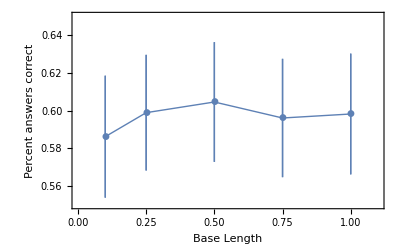

```mathematica
ErrorListPlot[#,Joined->True,PlotRange->{{0,1.1},{0.55,0.65}},Frame-> {True,True,False,False},FrameLabel->{"Base Length","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{ToExpression@#[[1,1]],Mean[#[[;;,2]]]},ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@Transpose[{#[[1,2]],Mean@#[[;;,-1]]}&/@GatherBy[#,#[[{2}]]&]&/@DataClnGraded,{2,1,3}])
```

### Percent correct vs. Angle Size

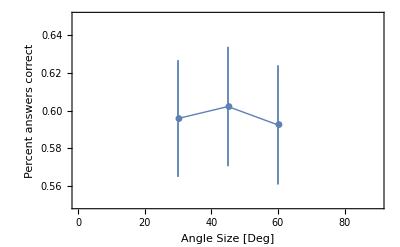

```mathematica
ErrorListPlot[#,Joined->True,PlotRange->{{0,90},{0.55,0.65}},Frame-> {True,True,False,False},FrameLabel->{"Angle Size [Deg]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{ToExpression@#[[1,1]],Mean[#[[;;,2]]]},ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@Transpose[{#[[1,1]],Mean@#[[;;,-1]]}&/@GatherBy[#,#[[{1}]]&]&/@DataClnGraded,{2,1,3}])
```

### Percent correct vs. Side length

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

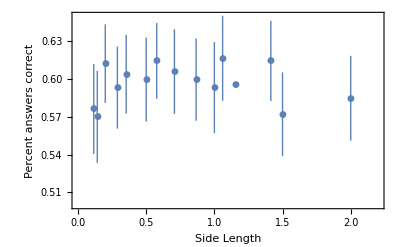

```mathematica
ErrorListPlot[#,(*Joined->True,*)PlotRange->{{0,2.2},{0.5,0.65}},Frame-> {True,True,False,False},FrameLabel->{"Side Length","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{#[[1,1]],Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&/@Transpose[Map[{(ToExpression@#[[1,2]])/Cos[ToExpression@#[[1,1]] Degree],Mean@#[[;;,-1]]}&,(GatherBy[#,#[[{1,2}]]&]&/@DataClnGraded),{2}],{2,1,3}])
```

### Percent correct vs. Question type

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

#### What’s being asked about

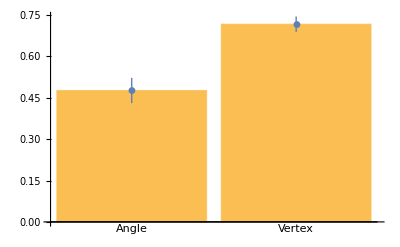

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Angle","Vertex"}],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[1]]=="angle",1,2],#[[2]]}&,{#[[1,3]],Mean@#[[;;,-1]]}&/@GatherBy[#,#[[{3}]]&]&/@DataClnGraded,{2}],First])]
```

#### What’s being manipulated

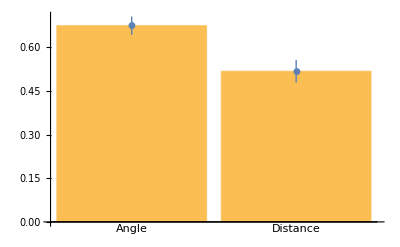

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Angle","Distance"}],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[1]]=="angle",1,2],#[[2]]}&,{#[[1,5]],Mean@#[[;;,-1]]}&/@GatherBy[#,#[[{5}]]&]&/@DataClnGraded,{2}],First])],First]
```

#### What’s being manipulated

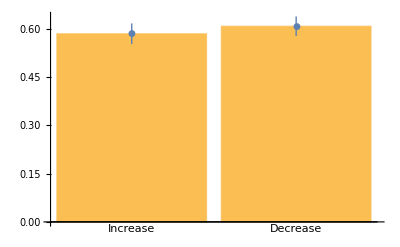

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Increase","Decrease"}],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[1]]=="increase",1,2],#[[2]]}&,{#[[1,4]],Mean@#[[;;,-1]]}&/@GatherBy[#,#[[{4}]]&]&/@DataClnGraded,{2}],First])],First]
```

#### Every Question Type Alone

```mathematica
rules={{"angle","increase","distance"}-> 1,{"angle","decrease","distance"}-> 2,{"angle","increase","angle"}-> 3,{"angle","decrease","angle"}->4,{"vertex","increase","distance"}->5,{"vertex","decrease","distance"}-> 6,{"vertex","increase","angle"}-> 7,{"vertex","decrease","angle"}-> 8};
```

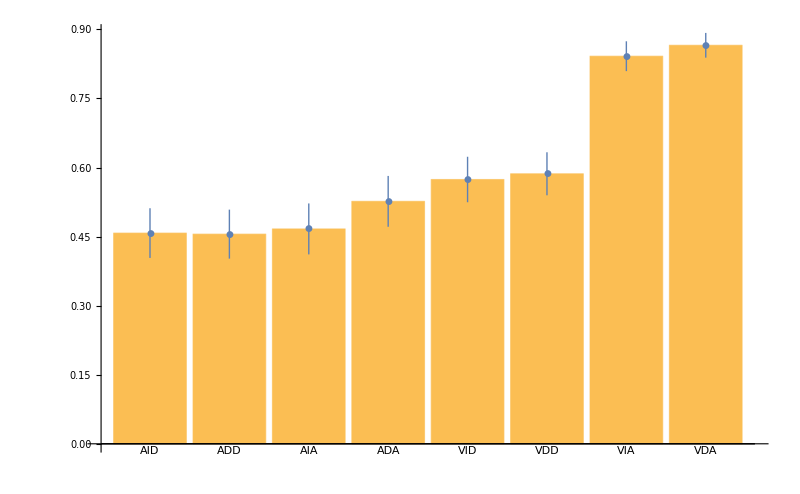

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"AID","ADD","AIA","ADA","VID","VDD","VIA","VDA"},ImageSize->800],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@GatherBy[Join@@(({#[[1,{3,4,5}]],Mean@#[[;;,-1]]}&/@GatherBy[#,#[[{3,4,5}]]&]&/@DataClnGraded)/.rules),First]],First]
```

## Response times

### Response times vs. Base length

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

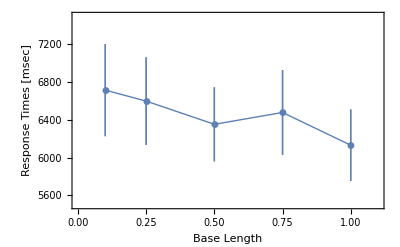

```mathematica
ErrorListPlot[#,Joined->True,PlotRange->{{0,1.1},{5500,7.5 10^3}},Frame-> {True,True,False,False},FrameLabel->{"Base Length","Response Times [msec]"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{ToExpression@#[[1,1]],Mean[#[[;;,2]]]},ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@Transpose[{#[[1,2]],Median@ToExpression@#[[;;,7]]}&/@GatherBy[#,#[[{2}]]&]&/@DataClnGraded,{2,1,3}])
```

### Response Times vs. Angle Size

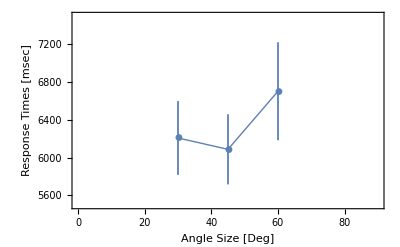

```mathematica
ErrorListPlot[#,Joined->True,PlotRange->{{0,90},{5.5 10^3,7.5 10^3}},Frame-> {True,True,False,False},FrameLabel->{"Angle Size [Deg]","Response Times [msec]"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{ToExpression@#[[1,1]],Mean[#[[;;,2]]]},ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@Transpose[{#[[1,1]],Median@ToExpression@#[[;;,7]]}&/@GatherBy[#,#[[{1}]]&]&/@DataClnGraded,{2,1,3}])
```

### Response Time vs. Side length

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

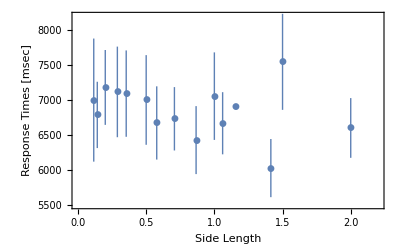

```mathematica
ErrorListPlot[#,(*Joined->True,*)PlotRange->{{0,2.2},{5.5 10^3,8.2 10^3}},Frame-> {True,True,False,False},FrameLabel->{"Side Length","Response Times [msec]"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{#[[1,1]],Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&/@Transpose[Map[{(ToExpression@#[[1,2]])/Cos[ToExpression@#[[1,1]] Degree],Median@ToExpression@#[[;;,7]]}&,(GatherBy[#,#[[{1,2}]]&]&/@DataClnGraded),{2}],{2,1,3}])
```